# PHSX 591 Solar Flares & CMEs

## Problem Set 1 Roy Smart Due Feb. 15th

```mathematica
Clear["Global`*"]
```

## Problem 1

### Part a.

#### The flux function for Figure 1a is given by

```mathematica
Ap = λ ArcTan[(y+b)/z]-λ ArcTan[(y+a)/z]+λ ArcTan[(y-a)/z]-λ ArcTan[(y-b)/z];
```

#### Define the assumptions for this expression

```mathematica
$Assumptions = λ >0 && a > 0  && z>0 && b > a  && c >0 && Ir < 0 && z >0
```

λ>0&&a>0&&z>0&&b>a&&c>0&&Ir<0&&z>0

#### Plot this function to see what it looks like

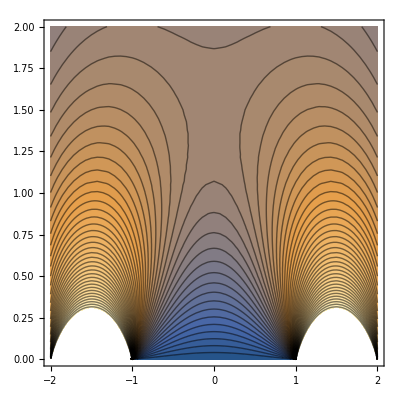

```mathematica
ContourPlot[Ap /. {b-> 2, a-> 1, λ->1},{y,-2,2},{z,0,2},Contours->50]
```

#### The X point is located where the magnetic field is equal to zero. Therefore, we will begin by taking a derivative of the flux function to determine the magnetic field.

```mathematica
Bp = Cross[Grad[Ap,{x,y,z}],{1,0,0}] //FullSimplify
```

{0,((a (1/(1+(a-y)^2/z^2)+1/(1+(a+y)^2/z^2))+y (-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2))-b/(1+(b-y)^2/z^2)-b/(1+(b+y)^2/z^2)) λ)/z^2,((-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2)) λ)/z}

#### Evaluate this field at y=0

```mathematica
Bpz = Bp /. y -> 0
```

{0,(((2 a)/(1+a^2/z^2)-(2 b)/(1+b^2/z^2)) λ)/z^2,0}

#### Find the height for which all components of the magnetic field are zero by solving the y-component for z

```mathematica
sol1aa=Solve[Bpz[[2]] == 0, z] //FullSimplify
```

{{z→-√(a b)},{z→√(a b)}}

#### Select the positive solution, since we are interested in the height of the X point above the photosphere

```mathematica
zx = sol1aa[[2,1,2]]
```

√(a b)

#### The flux between this X point and the origin is given by evaluating the flux function at this X point.

```mathematica
ψp12 = Ap /. {y-> 0,z-> zx} //FullSimplify
```

2 λ (-ArcTan[√(a/b)]+ArcTan[√(b/a)])

#### Check limit by expanding about a/b=0

```mathematica
Series[ψp12 /. b-> 1,{a,0,1}]/. a -> 0
```

π λ

#### Check another limit by expanding about a/b=1

```mathematica
Series[ψp12 /. b-> 1,{a,1,1}] /.a-> 1 //Quiet
```

0

### Part b.

#### The change in flux can be written as

```mathematica
Δψp12 = (ψp12 /. a -> a+ Δa ) - ψp12 //FullSimplify
```

2 λ (ArcTan[√(a/b)]-ArcTan[√(b/a)]+ArcTan[√(b/(a+Δa))]-ArcTan[√((a+Δa)/b)])

#### Expand the change in flux about Δa/a=0 to leading order.

```mathematica
Normal[Series[Δψp12/.{b-> 2a, a-> 1},{Δa,0,1}]] /. Δa -> Δa/a
```

-(√2 (1+√(1/a) √a) √(1/a) Δa λ)/(1+2 a)

### Part c.

#### The potential field after the wire is added is given by

```mathematica
A = Ap + Ics/c Log[(y^2 + (z+h)^2)/(y^2+(z-h)^2)]
```

λ ArcTan[(-a+y)/z]-λ ArcTan[(a+y)/z]-λ ArcTan[(-b+y)/z]+λ ArcTan[(b+y)/z]+(Ics Log[(y^2+(h+z)^2)/(y^2+(-h+z)^2)])/c

```mathematica
ContourPlot[A /. {b-> 2, a-> 1, λ->1, Ics->-0.01, c-> 1,h->√2},{y,-2,2},{z,0,3},Contours->150]
```

-Graphics-

#### Again, the null points are where the magnetic field is equal to zero. Start by calculating the new magnetic field for this new potential

```mathematica
B = Cross[Grad[A,{x,y,z}],{1,0,0}] //FullSimplify
```

{0,(4 h Ics (h^2+y^2-z^2))/(c (y^2+(h-z)^2) (y^2+(h+z)^2))+((a-y)/((a-y)^2+z^2)+(-b+y)/((b-y)^2+z^2)+(a+y)/((a+y)^2+z^2)-(b+y)/((b+y)^2+z^2)) λ,(8 h Ics y z)/(c (y^2+(h-z)^2) (y^2+(h+z)^2))+z (-1/((a-y)^2+z^2)+1/((b-y)^2+z^2)+1/((a+y)^2+z^2)-1/((b+y)^2+z^2)) λ}

#### Evaluate this field at y=0

```mathematica
By = (B /. y-> 0 )[[2]] // FullSimplify
```

(4 h Ics)/(c h^2-c z^2)+(2 a λ)/(a^2+z^2)-(2 b λ)/(b^2+z^2)

```mathematica
Series[By,{z,h,1}]
```

-(2 Ics)/(c (z-h))+(Ics/(c h)+(2 a λ)/(a^2+h^2)-(2 b λ)/(b^2+h^2))+(-Ics/(2 c h^2)-(4 a h λ)/((a^2+h^2)^2)+(4 b h λ)/((b^2+h^2)^2)) (z-h)+O[z-h]^2

#### Now solve for the height

```mathematica
h=zx
```

√(a b)

```mathematica
sol2=Solve[By  == 0,z] ;
zn1=sol2[[2,1,2]] //Simplify
zn2 = sol2[[4,1,2]] //Simplify
```

√((-√(a^5 b) Ics-√(a b^5) Ics-a^2 b c λ+a b^2 c λ+(a+b) √(a (a-b) b Ics (a Ics-b Ics+2 √(a b) c λ)))/(2 √(a b) Ics+(-a+b) c λ))

√(-(√(a^5 b) Ics+√(a b^5) Ics+a^2 b c λ-a b^2 c λ+(a+b) √(a (a-b) b Ics (a Ics-b Ics+2 √(a b) c λ)))/(2 √(a b) Ics+(-a+b) c λ))

```mathematica
znb1 = (zn1/.Ics -> c λ Ir) //FullSimplify
znb2 = (zn2 /. Ics -> c λ Ir) //FullSimplify
```

√((-a^2 b+a b^2-√(a^5 b) Ir-√(a b^5) Ir+(a+b) √(a (a-b) b Ir (2 √(a b)+a Ir-b Ir)))/(-a+b+2 √(a b) Ir))

√(-(a^2 b-a b^2+√(a^5 b) Ir+√(a b^5) Ir+(a+b) √(a (a-b) b Ir (2 √(a b)+a Ir-b Ir)))/(-a+b+2 √(a b) Ir))

```mathematica
zna1 = Series[znb1, {Ir,0,1}] // FullSimplify
zna2 = Series[znb2, {Ir,0,1}]//FullSimplify
```

√(a b)-((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))+((a+b)^2 Ir)/(4 (a-b))+O[Ir]^(3/2)

√(a b)+((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))+((a+b)^2 Ir)/(4 (a-b))+O[Ir]^(3/2)

```mathematica
znc1 = Normal[zna1] 
znc2 = Normal[zna2]
```

√(a b)-((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))+((a+b)^2 Ir)/(4 (a-b))

√(a b)+((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))+((a+b)^2 Ir)/(4 (a-b))

```mathematica
znd1 = znc1[[1]] + znc1[[2]] // FullSimplify
znd2 = znc2[[1]] + znc2[[2]] // FullSimplify
```

√(a b)-((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))

√(a b)+((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b))

```mathematica
A1 =A /. y-> 0/. z -> znd1  //Simplify
A2=A /. y-> 0/.z -> znd2 //Simplify
```

-2 λ ArcTan[a/(√(a b)-((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b)))]+2 λ ArcTan[b/(√(a b)-((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b)))]+(Ics Log[((-4 √(a-b) (a b)^(1/4)+√2 a √Ir+√2 b √Ir)^2)/(2 (a+b)^2 Ir)])/c

-2 λ ArcTan[a/(√(a b)+((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b)))]+2 λ ArcTan[b/(√(a b)+((a b)^(1/4) (a+b) √Ir)/(√2 √(a-b)))]+(Ics Log[((4 √(a-b) (a b)^(1/4)+√2 a √Ir+√2 b √Ir)^2)/(2 (a+b)^2 Ir)])/c

```mathematica
a1=Series[A1,{Ir,0,2}] //Simplify //Normal
```

-((a+b) Ics √Ir)/(√2 √(a-b) (a b)^(1/4) c)-(Ir (((a+b)^2 Ics)/(√(a b) c)-8 a λ+8 b λ))/(8 (a-b))+(Ir^2 (-((a+b)^4 Ics)/c+64 a^2 (a-b) √(a b) λ+64 (a-b) b^2 √(a b) λ))/(128 a (a-b)^2 b)-((a+b) Ir^(3/2) (a^2 Ics+2 a b Ics+b^2 Ics-24 a √(a b) c λ+24 b √(a b) c λ))/(24 √2 (a-b)^(3/2) (a b)^(3/4) c)+(-2 c λ ArcTan[√(a/b)]+2 c λ ArcTan[√(b/a)]+Ics (-ⅈ π+Log[(8 √(a b) (-a+b))/(a+b)^2]-Log[Ir]))/c

```mathematica
a2=Series[A2,{Ir,0,2}] //Simplify //Normal
```

((a+b) Ics √Ir)/(√2 √(a-b) (a b)^(1/4) c)-(Ir (((a+b)^2 Ics)/(√(a b) c)-8 a λ+8 b λ))/(8 (a-b))+(Ir^2 (-((a+b)^4 Ics)/c+64 a^2 (a-b) √(a b) λ+64 (a-b) b^2 √(a b) λ))/(128 a (a-b)^2 b)+((a+b) Ir^(3/2) (a^2 Ics+2 a b Ics+b^2 Ics-24 a √(a b) c λ+24 b √(a b) c λ))/(24 √2 (a-b)^(3/2) (a b)^(3/4) c)+(-2 c λ ArcTan[√(a/b)]+2 c λ ArcTan[√(b/a)]+Ics (Log[(8 (a-b) √(a b))/(a+b)^2]-Log[Ir]))/c

```mathematica
a1 == a2 //Simplify
```

24 √(a b) (-ⅈ (a b)^(1/4) Ics π+√2 a^2 c (Ir/(a-b))^(3/2) λ+(a b)^(1/4) Ics Log[(8 √(a b) (-a+b))/(a+b)^2])==1/(a-b)(√2 (a^3 Ics Ir √(Ir/(a-b))+3 a^2 b Ics Ir √(Ir/(a-b))+3 a b^2 Ics Ir √(Ir/(a-b))+b^3 Ics Ir √(Ir/(a-b))+24 (Ics √((a^5 b Ir)/(a-b))-Ics √((a b^5 Ir)/(a-b))+c Ir √((a b^5 Ir)/(a-b)) λ))+24 (a-b) (a b)^(3/4) Ics Log[(8 (a-b) √(a b))/(a+b)^2])

```mathematica
Log[-1]
```

ⅈ π

```mathematica
Ics (-ⅈ π+Log[(8 √(a b) (-a+b))/(a+b)^2]-Log[Ir])==Ics (Log[(8 (a-b) √(a b))/(a+b)^2]-Log[Ir]) //Simplify
```

Ics==0